```mathematica
Remove["Global`*"]
```

```mathematica
WPM=40;WPL=30;WPP=15;
```

```mathematica
q = 51; V0=(204/100)*10^(-8);
t0 = (q*(3*q-1)/V0)^(1/2);ϕ0=1; dϕ0=N[(((2*q)^(1/2))/t0),60];Ni=0;Nf=70;
```

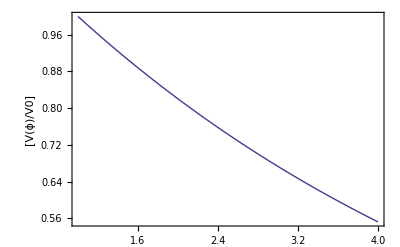

```mathematica
V[ϕ_] = V0*Exp[-((2/q)^(1/2))*(ϕ-ϕ0)];
DV[ϕ_] = D[V[ϕ],ϕ];
Plot[(V[ϕ]/V0),{ϕ,ϕ0,4},PlotRange->All,Frame->True, FrameLabel->{"[V(ϕ)/V0]"}]
```

```mathematica
H0 = ((1/3)*((dϕ0^2/2)+V[ϕ0]))^(1/2);
Dϕ0 = (dϕ0/H0);
```

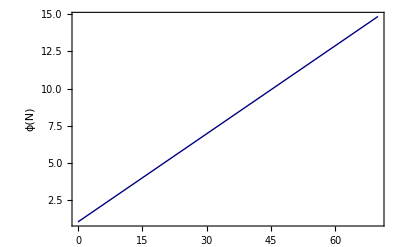

```mathematica
ϕSoln=NDSolve[{ϕ''[N1]+(3-ϕ'[N1]^2/2)*ϕ'[N1]+(DV[ϕ[N1]]/(2*V[ϕ[N1]]))*(6-(ϕ'[N1])^2)==0,ϕ[Ni]==ϕ0,ϕ'[Ni]==Dϕ0},ϕ,{N1,Ni,Nf},MaxSteps->1000000, WorkingPrecision->WPM];
ϕ[N1_]=ϕ[N1]/.Flatten[ϕSoln];
Plot[ϕ[N1],{N1,Ni,Nf},Frame->True,PlotRange->All,FrameLabel->{"ϕ(N)"},PlotStyle->{Darker[Blue,0.5]}]
```

```mathematica
toFile = Table[{" ",N[N1,10] ,N[ϕ[N1],10] ," "},{N1,Ni,Nf,(Nf-Ni)/100000}]//N
Export["~/Github/project_work/power_law/power_spectrum/data_files/phi_vs_N_mathematica.txt",toFile];
```

{{ ,0.,1., },{ ,0.0007,1.00014, },{ ,0.0014,1.00028, },«99995»,{ ,69.9986,14.8618, },{ ,69.9993,14.8619, },{ ,70.,14.8621, }}

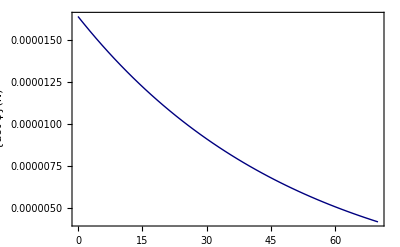

```mathematica
H[N1_]=(V[ϕ[N1]]/(3-((ϕ'[N1])^2)/2))^(1/2);
Plot[{H[N1]*ϕ'[N1]},{N1,Ni,Nf},Frame->True, PlotRange->All, FrameLabel->{"{dot ϕ}(N)"},PlotStyle->{Darker
[Blue,0.5]}]
```

```mathematica
toFile =Table[{" ",N[N1,10],N[H[N1],10]," "},{N1,Ni,Nf,(Nf-Ni)/100000}]//N;
Export["~/Github/project_work/power_law/power_spectrum/data_files/H_vs_N_mathematica.txt",toFile];
```

```mathematica
toFile = Table[{" ",N[N1,10],N[H'[N1]*10^6,10]," "},{N1,Ni,Nf,(Nf-Ni)/100000}]//N;
Export["~/Github/project_work/power_law/power_spectrum/data_files/DH_vs_N_mathematica.txt",toFile];
```

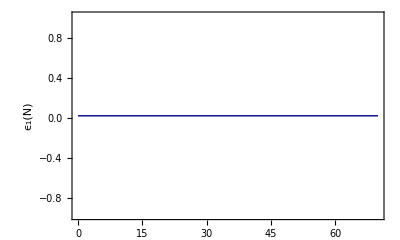

```mathematica
ϵ1[N1_] =((ϕ'[N1])^2/2);
Plot[ϵ1[N1],{N1,Ni,Nf},Frame->True, PlotRange->All, AspectRatio->0.6,FrameLabel->{"\!\(\*SubscriptBox[\(ϵ\),\(1\)]\)(N)"},PlotStyle->{Darker[Blue, 0.5]}]
```

```mathematica
toFile=Table[{" ",N[N1,10],N[ϵ1[N1],10]," "},{N1,Ni,Nf,(Nf-Ni)/100000}]//N;
Export["~/Github/project_work/power_law/power_spectrum/data_files/eps_vs_N_mathematica.txt",toFile];
```

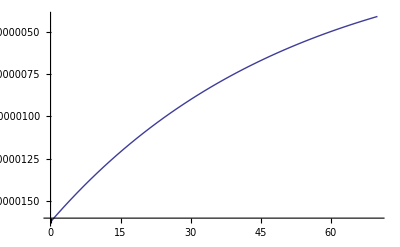

```mathematica
Plot[H'[N1],{N1,Ni,Nf}]
```

```mathematica
ai = 10^(-5);
A[N1_] = ai*Exp[N1]
```

ⅇ^N1/100000

```mathematica
toFile = Table[{k = 10^(y);N[k,10],
Nics=N1/.FindRoot[k==(10^2*A[N1]*H[N1]),{N1,Ni,Nf},WorkingPrecision->WPL];N[Nics],
Nshss=N1/.FindRoot[k==(10^(-3)*A[N1]*H[N1]),{N1,Ni,Nf},WorkingPrecision->WPL];N[Nshss],
hkSoln = NDSolve[{hk''[N1]+hk'[N1]*(H'[N1]/H[N1]+3)+hk[N1]*(k/(H[N1]*A[N1]))^2==0, hk[Nics]==1/((2*k)^(1/2)*A[Nics]),hk'[Nics]==-I*(k/2)^(1/2)/(A[Nics]^2*H[Nics])-1/(A[Nics]*(2*k)^(1/2))},hk,{N1,Nics,Nshss}, InterpolationOrder->All,MaxSteps->10000000, WorkingPrecision->WPP];
(*hk[N_] = hk[N]/.hkSoln;*)
N[2*(k^3/(2*Pi^2))*(Abs[hk[Nshss]/.Flatten[hkSoln]]^2)]*10^(10)},{y,-(60/10),-(0/10),1/2}]
```

{{1.×10^-6,2.54198,14.2852,2.58219},{3.16227766×10^-6,3.7163,15.4595,2.46597},{0.00001,4.89062,16.6338,2.35498},{0.0000316227766,6.06494,17.8081,2.24899},{0.0001,7.23925,18.9824,2.14777},{0.000316227766,8.41357,20.1568,2.0511},{0.001,9.58789,21.3311,1.95879},{0.00316227766,10.7622,22.5054,1.87063},{0.01,11.9365,23.6797,1.78644},{0.0316227766,13.1108,24.854,1.70603},{0.1,14.2852,26.0283,1.62925},{0.316227766,15.4595,27.2027,1.55592},{1.,16.6338,28.377,1.48583}}

```mathematica
Export["~/Github/project_work/power_law/power_spectrum/data_files/tps_mathematica.txt",toFile]
```

~/Github/project_work/power_law/power_spectrum/data_files/tps_mathematica.txt